```mathematica
Remove["Global`*"]
```

```mathematica
f[x_]:=a x(1-x)
```

```mathematica
xs=(a-1)/a
```

(-1+a)/a

```mathematica
ϵ2=f[xs+ϵ]-xs//Simplify//Expand
```

2 ϵ-a ϵ-a ϵ^2

```mathematica
Series[f[xs+ϵ2]-xs,{ϵ,0,3}]/.a->3
```

ϵ-18 ϵ^3+O[ϵ]^4

```mathematica
Series[f[f[x]],{x,0,4}]
```

a^2 x+(-a^2-a^3) x^2+2 a^3 x^3-a^3 x^4+O[x]^5

```mathematica
(f[f[x]]-x)/(x(x-(a-1)/a))//FullSimplify//Expand
```

-a-a^2+a^2 x+a^3 x-a^3 x^2

```mathematica
x1=(a+1+√(a^2-2a-3))/(2a);
x2=(a+1-√(a^2-2a-3))/(2a);
```

```mathematica
f'[x1]//Simplify
```

-1-√(-3-2 a+a^2)

```mathematica
f'[x2]//Simplify
```

-1+√(-3-2 a+a^2)

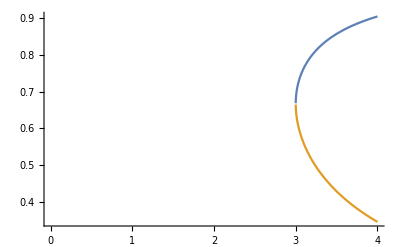

```mathematica
Plot[{(a+1+√(a^2-2a-3))/(2a),(a+1-√(a^2-2a-3))/(2a)},{a,0,4}]
```